--- 单位脉冲响应 h[n] 矩阵 ---

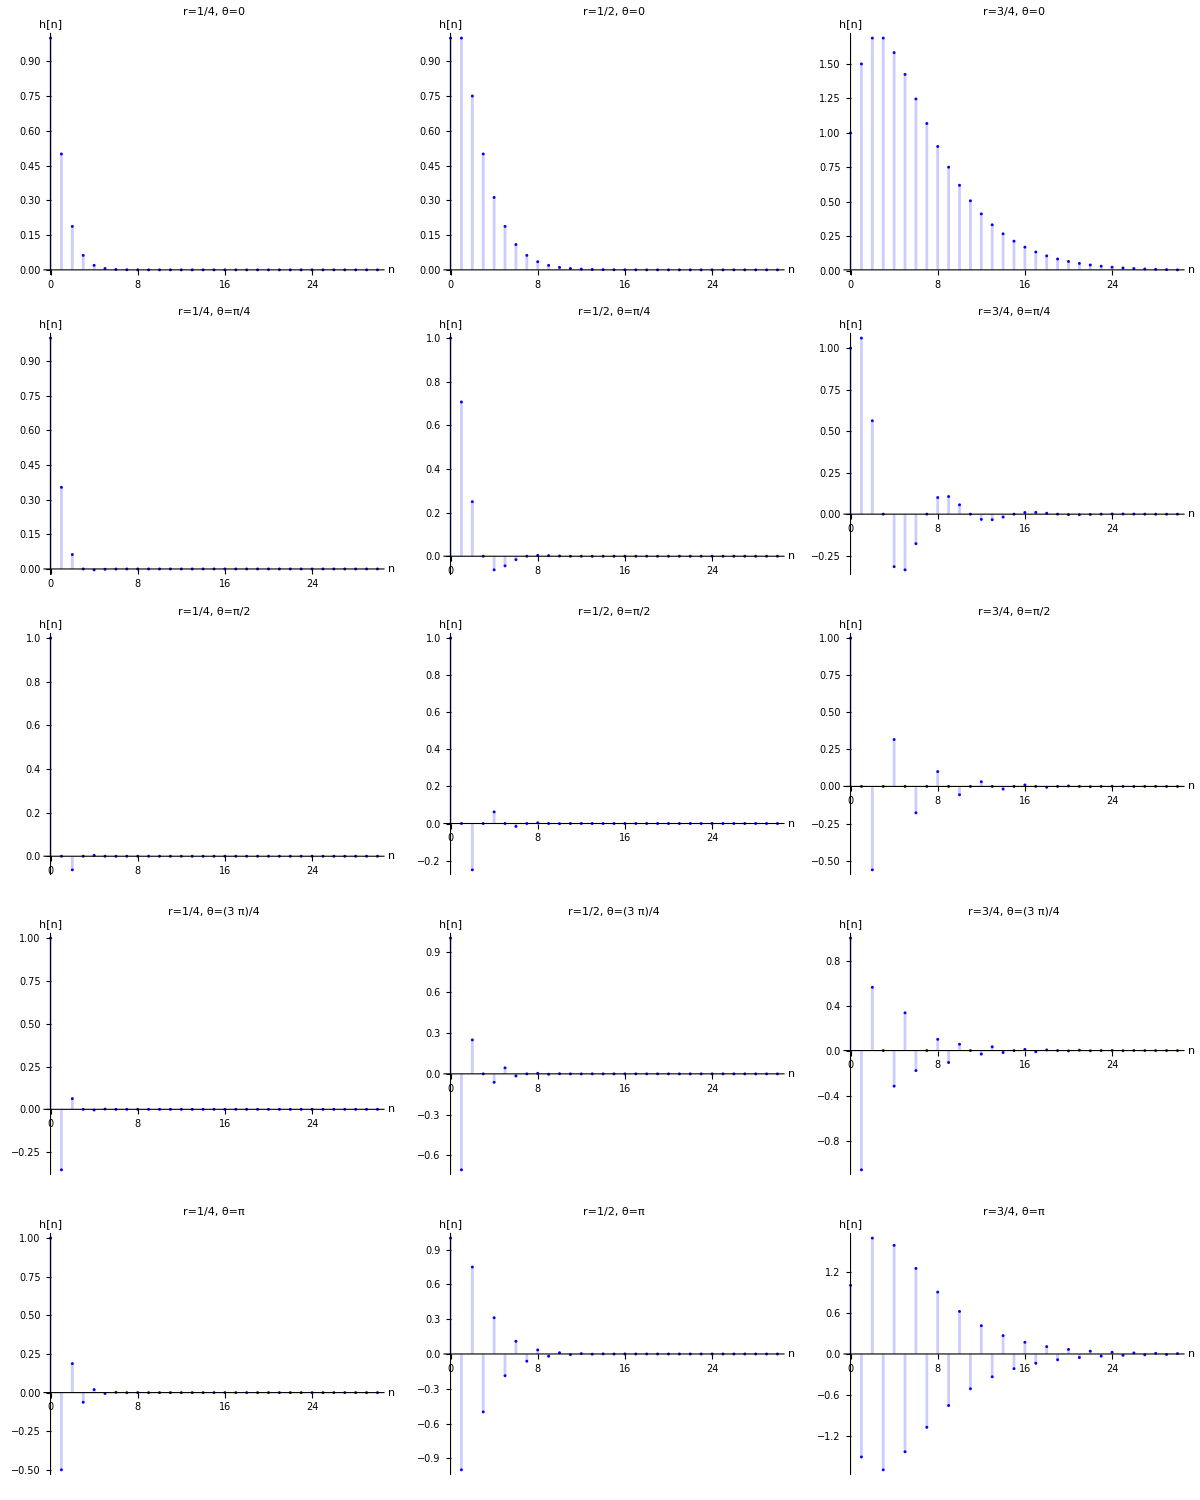

--- 单位阶跃响应 s[n] 矩阵 ---

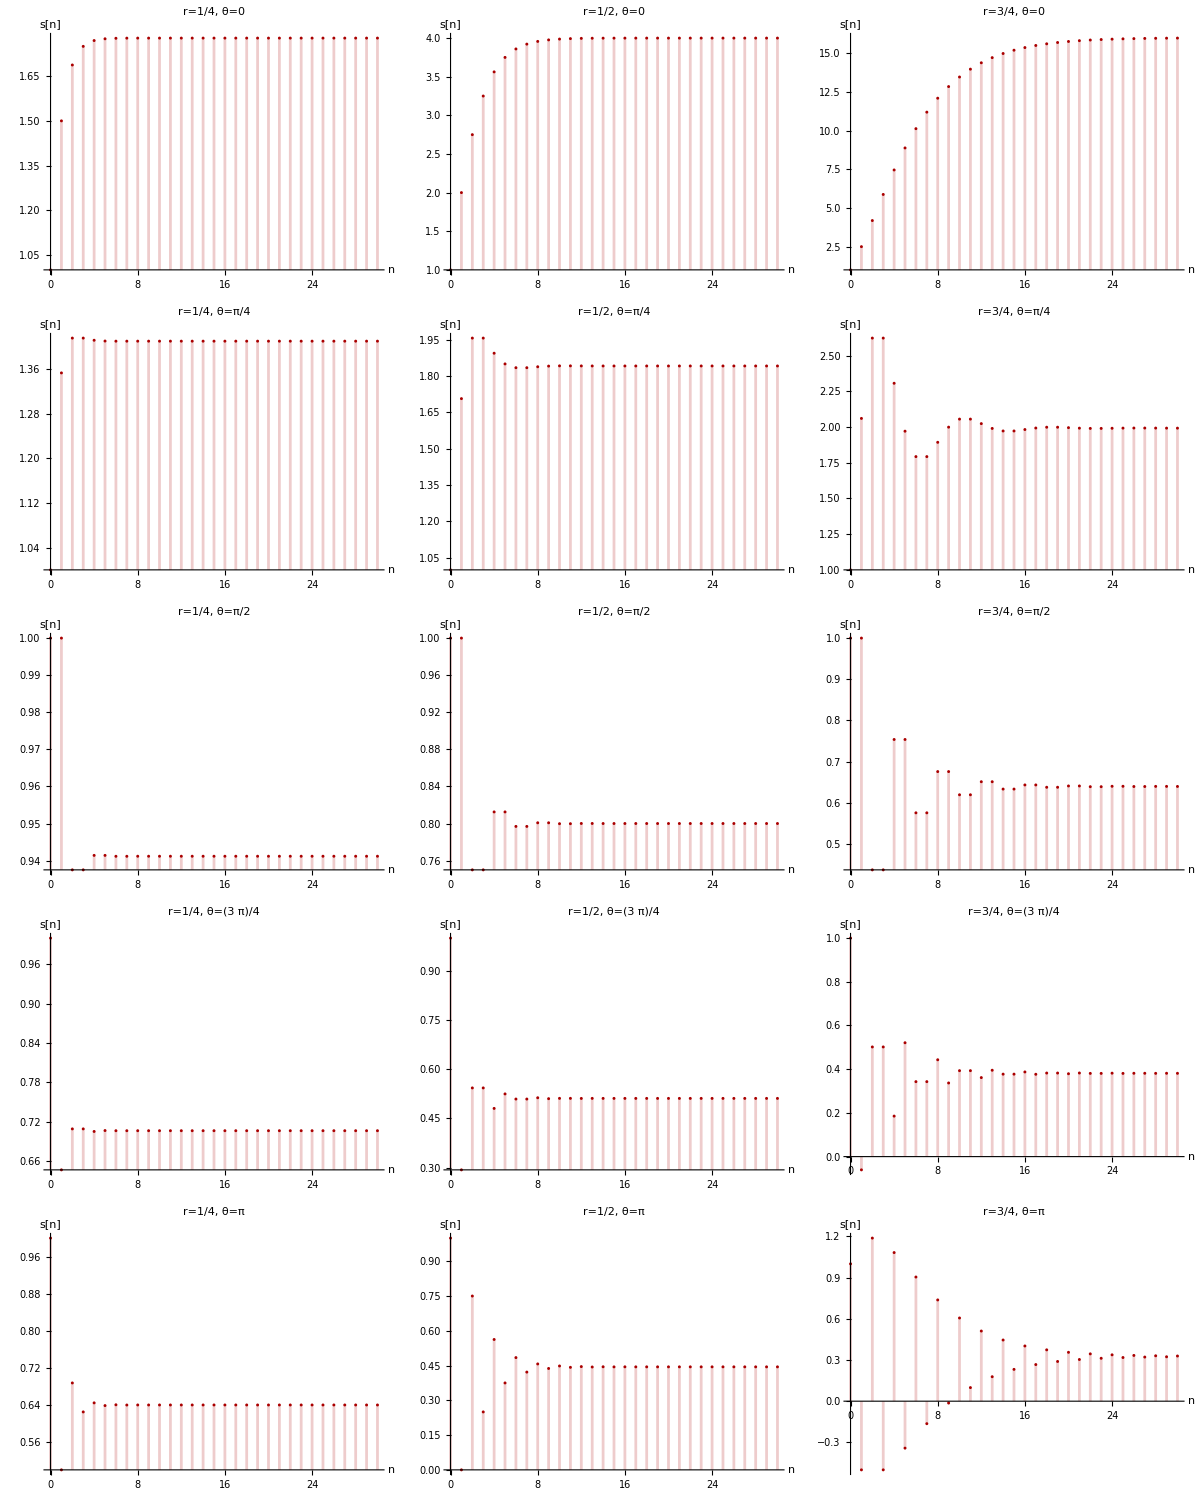

```mathematica
(*1. 定义解析形式的响应函数*)(*单位脉冲响应 h[n]*)h[n_,r_,theta_]:=Which[theta==0,(n+1) r^n,theta==Pi,(n+1) (-r)^n,True,r^n*Sin[(n+1) theta]/Sin[theta]];

(*单位阶跃响应 s[n] (通过对 h[k] 求和得到)*)
s[n_,r_,theta_]:=Sum[h[k,r,theta],{k,0,n}];

(*2. 设定参数组合 (匹配图片中的 3x5 布局)*)
rList={1/4,1/2,3/4};
thetaList={0,Pi/4,Pi/2,3*Pi/4,Pi};

(*3. 批量生成图形函数*)
GeneratePlots[type_]:=Table[DiscretePlot[If[type=="Impulse",h[n,rVal,thetaVal],s[n,rVal,thetaVal]],{n,0,30},PlotRange->All,Filling->Axis,PlotMarkers->{Automatic,3},PlotStyle->If[type=="Impulse",Blue,Darker[Red]],PlotLabel->Style[Row[{"r=",rVal,", θ=",thetaVal}],10,Bold],ImageSize->200,AxesLabel->{"n",If[type=="Impulse","h[n]","s[n]"]}],{thetaVal,thetaList},{rVal,rList}];

(*4. 分别展示脉冲响应和阶跃响应的矩阵*)
Print["--- 单位脉冲响应 h[n] 矩阵 ---"];
Grid[GeneratePlots["Impulse"],Frame->All,Spacings->{1,1}]

Print["--- 单位阶跃响应 s[n] 矩阵 ---"];
Grid[GeneratePlots["Step"],Frame->All,Spacings->{1,1}]
```